Sorbonne Université  |               |                                     Atelier de Recherche Encadrée UE LU1SXARE ”Mesures”

__________________________________________________________________________

M 1 : Introduction à Mathematica
__________________________________________________________________________

## Exercices

Le fichier doit être renommé exactement comme ceci :
	M1VotrenomPrenom.nb
Cela permet à vos enseignants de s’y retrouver et de ne pas avoir à renommer tous les fichiers. Merci.
	Votrenom avec une seule majuscule
	Prenom avec une seule majuscule
	Pas de blanc, ni souligné, ni accent, ni symbole particulier
Ce fichier doit être déposé sur MOODLE à la fin de la séance, et/ou avant la fin de la semaine de la séance.

NB : Ce fichier comprend PLUSIEURS pages ! qui sont toutes à traiter !!

## I. Interface

### A. Mise en forme

#### 1. Les cellules et leur hiérarchie

Inscrire votre nom et prénom, en rouge,  dans une cellule titre. Pour cela créer une nouvelle cellule, puis aller dans l’onglet Format, puis Style pour sélectionner  le titre et Text Color pour sélectionner  la couleur.

Caldeira Ribeiro Cruz Isabela

## II. Un tour introductif

→ Expliquer ce qui se passe quand vous validez les cellules : Réfléchissez et donner par écrit les propriétés du logiciel. Les solutions sont données dans les cellules cachées de M1IntroductionMMaTxt.nb

### A. Opérations de base (symboliques avec précision arbitraire)

```mathematica
Bonjour!
```

Bonjour!

#### 1. Élémentaire

```mathematica
1+1
```

2

```mathematica
4a+5a
```

9 a

```mathematica
Cos[Pi]
```

-1

```mathematica
Cos[x] /. x -> π
```

-1

```mathematica
3x + 2 x
```

5 x

#### 2. Les trois opérations :

```mathematica
31 5
315/14
3^100
```

155

45/2

515377520732011331036461129765621272702107522001

```mathematica
3^1000
```

#### 3. Valeurs numériques approchées N[] :

```mathematica
N[315/14]
N[3^100]
N[3^100, 20]
```

22.5

5.15378×10^47

5.1537752073201133104×10^47

#### 4. Quelques tests utiles à partir de calcul de puissances pour comprendre

```mathematica
3^100;//AbsoluteTiming
```

{0.000042,Null}

```mathematica
3^1000;//AbsoluteTiming
```

{0.0000465,Null}

```mathematica
3^10000;//AbsoluteTiming
```

{0.0000679,Null}

```mathematica
3^100000;//AbsoluteTiming
```

{0.0003529,Null}

```mathematica
3^1000000;//AbsoluteTiming
```

{0.0054706,Null}

```mathematica
3^10000000;//AbsoluteTiming
```

{0.0804095,Null}

```mathematica
3^100000000;//AbsoluteTiming
```

{0.974512,Null}

```mathematica
(* NB : pas de ";" *)
N[3^100000000]//AbsoluteTiming
N[3.^100000000]//AbsoluteTiming
```

{0.975719,2.96460095196382×10^47712125}

{0.0000317,2.964600951548×10^47712125}

#### 5. Exemples récapitulatifs

```mathematica
N [Pi]
```

3.14159

```mathematica
π //N
```

3.14159

```mathematica
N[π,30]
```

3.14159265358979323846264338328

```mathematica
N[π,2000]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491298336733624406566430860213949463952247371907021798609437027705392171762931767523846748184676694051320005681271452635608277857713427577896091736371787214684409012249534301465495853710507922796892589235420199561121290219608640344181598136297747713099605187072113499999983729780499510597317328160963185950244594553469083026425223082533446850352619311881710100031378387528865875332083814206171776691473035982534904287554687311595628638823537875937519577818577805321712268066130019278766111959092164201989380952572010654858632788659361533818279682303019520353018529689957736225994138912497217752834791315155748572424541506959508295331168617278558890750983817546374649393192550604009277016711390098488240128583616035637076601047101819429555961989467678374494482553797747268471040475346462080466842590694912933136770289891521047521620569660240580381501935112533824300355876402474964732639141992726042699227967823547816360093417216412199245863150302861829745557067498385054945885869269956909272107975093029553211653449872027559602364806654991198818347977535663698074265425278625518184175746728909777727938000816470600161452491921732172147723501414419735685481613611573525521334757418494684385233239073941433345477624168625189835694855620992192221842725502542568876717904946016534668049886272327917860857843838279679766814541009538837863609506800642251252051173929848960841284886269456042419652850222106611863067442786220391949450471237137869609563643719172874677646575739624138908658326459958133904780275901

### B. Opérations de base (numériques)

```mathematica
(10.2-3.1)*6.2/2.9
```

15.1793

```mathematica
(2+3I)*(4-5I)
```

23+2 ⅈ

### C. Nombres et Fonctions élémentaires

#### 1. Quelques constantes mathématiques

→ Saisir dans une cellule input (sans faire de copier coller !!!)

- le nombre π

```mathematica
N[Pi]
```

3.14159

- le nombre e

```mathematica
N[e]
```

e

- le nombre imaginaire i

```mathematica
N[I]
```

0.+1. ⅈ

- l'infini ∞ :

```mathematica
N[∞]
```

∞

#### 2. Quelques fonctions mathématiques

Mathematica dispose de nombreuses fonctions prédéfinies dont le nom suit la règle Nom[] :

→ Comment écrit-on dans une cellule input (sans faire de copier coller non plus !!!) les fonctions suivantes :

- racine carrée : √x

```mathematica
Sqrt[x]
```

√x

- exponentielle : e^x

```mathematica
Exp[x]
```

ⅇ^x

- logarithme népérien : ln(x)

```mathematica
Log[x]
```

Log[x]

- logarithme en base b : log_b(x)  (le plus souvent, b=10)

```mathematica
Log[b,x]
```

Log[x]/Log[b]

- fonctions trigonométriques :

```mathematica
Cos
```

Cos

```mathematica
Sin
```

Sin

```mathematica
Tan
```

Tan

- fonctions trigonométriques inverses :

```mathematica
ArcCos
```

ArcCos

```mathematica
ArcSin
```

ArcSin

```mathematica
ArcTan
```

ArcTan

- valeur absolue : |x|

```mathematica
Abs[x]
```

Abs[x]

- factorielle : n !

```mathematica
n!
```

n!

→ Sélectionnez la fonction Cos[] et tapez sur F1 (sous PC) ou ⌘ F (sous Mac) pour afficher la page d'aide de cette fonction.

→ Explorez d’autres fonctions avec la rubrique SEE ALSO “ref/ArcCos”

→ Revenez à la page d’aide précédente, et explorez TUTORIALS “tutorial/SomeMathematicalFunctions” qui donne une petite liste des fonctions élémentaires

→ Revenez à la page d’aide précédente, et explorez MORE ABOUT  “guide/SomeMathematicalFunctions” qui donne la liste des fonctions élémentaires

### D. Fonctions

#### 1. Programmation procédurale et fonctionnelle

#### 2. Mode d’utilisation d’une fonction

En dehors de la notation fonctionnel standard Nom[argument1, argument2, ...], il y a trois façons d’utiliser ou de noter les fonctions :
		Prefix
		Infix
		Postfix

→ Quelles sont les notations Infix pour l’addition “+“ , la multiplication “*”, la soustraction “-”, la division “/”, la puissance, →,   /. .... ?

```mathematica
x ~ Plus ~ y
```

x+y

```mathematica
x~Times ~y
```

x y

```mathematica
x~ Subtract~y
```

x-y

```mathematica
x ~ Divide~y
```

x/y

```mathematica
x ~ Power ~ y
```

x^y

#### 3. Composition de fonctions

→ Saisir dans une cellule “Input”, et constater que la hiérarchie d’indentation est automatiquement respectée à chaque retour à la ligne :

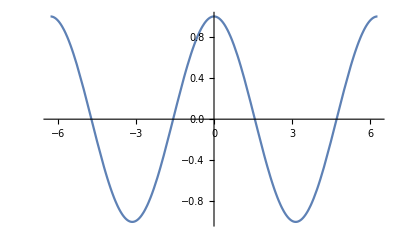

```mathematica
Plot[Cos[x],{x,-2 π,2 π}]
```

Plot[
 Cos[x],
 {x, -2 π, 2 π}
 ]

Idem...

```mathematica
Manipulate[Plot[Cos[a x+b],{x,-2 π,2 π}],{a,1,10},{b,0,2 π}
]
```

Manipulate[
 Plot[
  Cos[a x + b],
  {x, -2 π, 2 π}
  ],
 {a, 1, 10},
 {b, 0, 2 π}
 ]

→ Puis jouez avec les curseurs !

#### 4. Arguments et Options des Fonctions : tracer de courbes

Les fonctions ont généralement des arguments obligatoires, et un certain nombre d’Options que l’on peut ou non rajouter pour préciser la fonction. Étudions la fonction très utile Plot[] au travers des exemples suivants :

→ Tracer, ⅇ^-x Sin[2 π x]

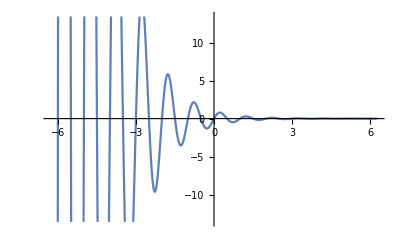

```mathematica
Plot[Exp[-x]*Sin[2*Pi*x],{x,-2 π,2 π}]
```

→ Idem en rajoutant en option AxesLabel→{“Time”,”Ampl.”}, pour spécifier les axes.
Elle consiste à remplir avec les contenus donnés dans la liste {“Time”,”Ampl.”} la variable AxesLabel :

→ Tracé de plusieurs fonctions sur le même graphe au moyen d’une liste de fonctions :
		 { ⅇ^-x Sin[2 π x],Exp[-x],-Exp[-x] }

→ Mettez des couleurs

#### 5. Définition de nouvelle fonction par l’utilisateur

→ Définissez la fonction h(x)=(a x)/(b + x), pour cela écrire, puis valider la fonction pour qu’elle soit connue du noyau :

```mathematica
h[x_] := (a*x)/ (b+x) 

h[2]
```

(2 a)/(2+b)

#### 6. Éléments d’étude de fonction

→ Calcul de la dérivée première de h :

```mathematica
h'[s]
```

```mathematica
-(a s)/(b+s)^2+a/(b+s)
```

-(a s)/(b+s)^2+a/(b+s)

```mathematica
D[h[x],{x, 1}]
```

→ Calcul des asymptotes :

```mathematica
Limit[h[x],x->∞]
```

a

→ Calcul de valeurs particulières par résolution d’équations :
recherchez la valeur de s pour laquelle h[s] est la moitié de la valeur maximale atteignable.

```mathematica
Solve[h[s]==a/2,s]
```

{{s→b}}

→ Tracer la courbe de h(x) pour a et b valant respectivement 10.0 et 5.0 dans une région pertinente du plan :

10.

5.

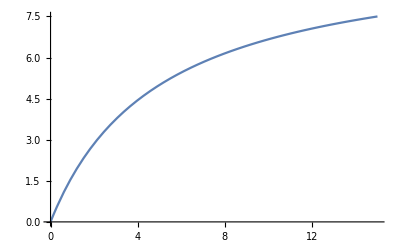

```mathematica
a = 10.0
b = 5.0

Plot[h[x], {x,0, 15}]
```

→ Est-ce que la fonction h(x) a des singularités  ?
Vu la fonction de limite on voir que le limite de cette fonction est en a et dans ce cas a est égal à 10. Et donc la singularité est -5

### E. Graphiques 2D, 3D, sons et animations

#### 1. Représentation graphique

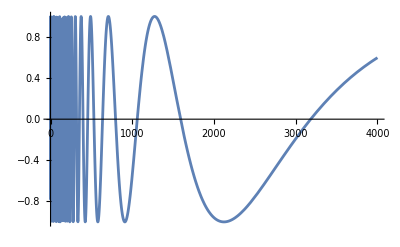

```mathematica
Plot[Sin[10000/t],{t,0,4000}]
```

Mais on arrive toujours à mettre le système en difficulté (Expliquer pourquoi ?):

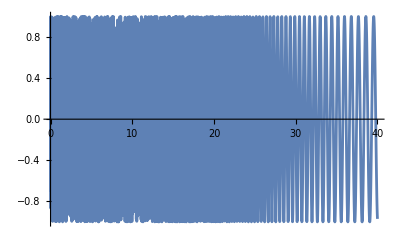

-Graphics-

```mathematica
Plot[Sin[10000/t],{t,0,40}]
```

#### 2. Représentation sonore

On peut d’ailleurs l’écouter, pour ce convaincre de la pathologie de la fonction en ce point. On remarquera que les singularités du type 1/0 ne sont pas un obstacle, ce qui est très appréciable.

```mathematica
Play[Sin[10000/t],{t,-2,-0.001}]
```

-Graphics-

#### 3. Tracé de fonction en 3 dimensions - Animation 3D

Sur le modèle de II.E.3, tracer une fonction simple en 3D.
En faire ensuite un Manipulate.

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

## Devoir à faire à la maison : CC1 (à déposer dans Moodle pour la prochaine séance)

1.  Définir dans Mathematica la densité de probabilité de la loi normale d’espérance μ et d’écart type σ que l’on notera gaussian.

```mathematica
gaussian[x_, μ_,σ_]:= 1/(Sqrt[2Pi]σ)Exp[-(x-μ)^2/(2σ^2)]
```

2. En utilisant la fonction notée gaussian définie ci-dessus, définir dans Mathematica la loi normale centrée réduite ou loi normale standard d’espérance nulle et d’écart type unité que l’on notera gaussianStandart.

```mathematica
gaussianStandart[x_] := gaussian[x,0,1]
```

3. Représenter graphiquement la fonction gaussianStandart.

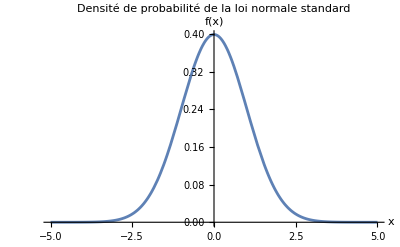

```mathematica
Plot[gaussianStandard[x],{x,-5,5}, PlotRange-> All, AxesLabel-> {"x","f(x)"},PlotLabel -> "Densité de probabilité de la loi normale standard"]
```

4. Calculer numériquement l’intégrale de la fonction gaussianStandart sur l’intervalle [-1, 1], [-2,2], [-3, 3] et sur son domaine de
définition.

```mathematica
integralInterval1 = NIntegrate[gaussianStandard[x], {x,-1,1}]
integralInterval2 = NIntegrate[gaussianStandard[x], {x,-2,2}]
integralInterval3 = NIntegrate[gaussianStandard[x], {x,-3,3}]
integralIntervalAll = NIntegrate[gaussianStandard[x], {x,-Infinity,Infinity}]
```

0.682689

0.9545

0.9973

1.

5. Définir la fonction de répartition de la loi normale centrée réduite. C’est une fonction de variable notée x qui représente l’intégrale de la fonction gaussianStandart sur l’intervalle [-infini , x].

```mathematica
integraleGaussian[x_] := NIntegrate[gaussianStandart[y],{y,-Infinity,x}]
```

6. Intégrer symboliquement la fonction notée gaussian sur son domaine de définition

```mathematica
symbolic = Integrate[gaussian[x,μ,σ],{x,-Infinity,Infinity}]
```

1

1